Risk Plots

## Unconstrained solutions

Plots that show the boundary of the feasible set, then draw in traces of solutions for iid mean process (typical of spike-and-slab Bayesian model).

Transfer file from server.  Parsing of parameter values, with special cases... 
	alpha = defines oracle		 		0 mins LS risk, and 1 mins risk, and other mins testimator risk
	beta = rate used by bidder if geometric		0 for universal (if omega=0, then bid = beta/n)
	omega = payout				0 indicates fixed bidding
	scale = scale parameter of universal distribution

### Functions for plotting and reading data ...

Idea is to make a file name based on parameter values.  Keep the name and parameter values as the first two items in a list with the data last.

```mathematica
Clear[fmt, getAlpha, getBeta,getN, getOmega, makeID, getData];

fmt[x_]:=With[{s= ToString[Round[100x]]},
If[StringLength[s]>1,s,StringJoin["0",s]]
]

makeID[α_,β_,ω_, scale_, n_] :=
{StringJoin["summary_risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]],
{α,β,ω,scale,n}
}

getAlpha[{_,parms_,_}] :=getAlpha[parms]
getAlpha[{α_,_,_,_,_}] :=α

getBeta[{_,parms_,_}] :=getBeta[parms]
getBeta[{_,β_,_,_,_}] :=β

getN[{_,parms_,_}] :=getN[parms]
getN[{_,_,_,_,n_}] :=n

getOmega[{_,parms_,_}]:=getOmega[parms]
getOmega[{_,_,ω_,_,_}]:=ω


getData[{name_,parms_},figureNumber_,server_]:=Module[
{f=ToString[figureNumber],
fullName,x},
fullName=StringJoin[" ~/C/bellman/figures/f",f,"1/",name];
If[StringLength[server]>1,
<<(StringJoin["!scp ",server,"C/bellman/figures/f",f,"/",name, fullName])];
x= Import[StringJoin["~/C/bellman/figures/f",f,"/",name], "Table"];
Print["found dimensions ", Dimensions[x]];
{name,parms,Sort[x,#1⟦3⟧<#2⟦3⟧&]} (* sort on angle *)
]
```

The function pickColumns adds 1 and flips sign to make work with log/log plot.

```mathematica
Clear[pickColumns, drawFeasibleSet,drawLogFeasibleSet];

pickColumns[simres_] := 1 -(#1⟦{7,8}⟧&)/@ simres

drawFeasibleSet[{name_,{α_,β_,ω_,σ_,n_},simres_},{join_:False,color_:Blue}]:=Module[
{xy =pickColumns[simres]},
ListPlot[xy,
Joined->join,
PlotRange->{{0,1.05Max[xy]},{0,1.05Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{simres⟦1,1⟧,If[ω==0,
StringJoin["Bonferroni(",ToString[β],")"],
simres⟦1,2⟧]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10},
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]

drawLogFeasibleSet[{name_,{α_,β_,ω_,σ_,n_},simres_},{join_:False,color_:Blue}] := Module[
{xy=pickColumns[simres]},
ListLogLogPlot[xy,
Print["2 log n =",2.Log[n]];
Joined->join,
PlotRange->{{1,1.2Max[xy]},{1,1.15Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{simres⟦1,1⟧,If[ω==0,
StringJoin["Bonferroni(",ToString[β],")"],
simres⟦1,2⟧]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω],")"],
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->10}, 
Epilog->{ (* LogLogPlot exponentiates all before drawing, as if these are on log scale *)
Orange,Line[{{0.01,0.01},{100,100}}],
Red, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}],
color,(*Arrow[Log[xy]]*)}]
]
```

```mathematica
Clear[drawFeasibleSets];

drawFeasibleSets[simres_List, title_,labels_]:=Module[
{xy =(pickColumns[#⟦3⟧]&)/@simres,
colors=GrayLevel/@Range[0.7,0.3,-0.4/Length[simres]],
legend= getOmega/@simres
},
ListPlot[xy,
Joined->True,
AspectRatio->1,
PlotStyle->colors,AxesLabel->labels,PlotLabel-> title,
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->12},
PlotLegends->SwatchLegend[legend, LegendLabel-> "ω"],
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]
```

### Figure 1 Feasible risks for varying ω, with RI oracle

The data that is produced has a list of 3 items
	file name
	parameter values (as alpha, beta, omega, scale and n)
	simulation results.

```mathematica
id = With[
{α=1,β=0.1,scale=2,n=500},
makeID[α,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

f1Data=Table[getData[id⟦i⟧,1,""],{i,1,4}];
```

{{summary_risk_alpha100_beta10_omega05_scale2_n500,{1,0.1,0.05,2,500}},{summary_risk_alpha100_beta10_omega25_scale2_n500,{1,0.1,0.25,2,500}},{summary_risk_alpha100_beta10_omega50_scale2_n500,{1,0.1,0.5,2,500}},{summary_risk_alpha100_beta10_omega75_scale2_n500,{1,0.1,0.75,2,500}}}

found dimensions {56,8}

found dimensions {56,8}

found dimensions {56,8}

«1 more identical outputs»

Look for the angle where risk increases suddenly.

```mathematica
f1Data[[4,3]]//TableForm
```

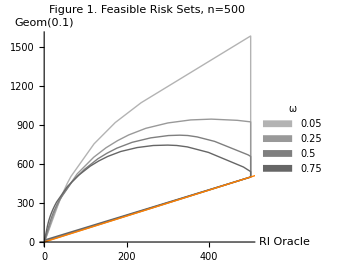

```mathematica
With[{β=ToString[getBeta[f1Data⟦1⟧]]},
drawFeasibleSets[f1Data, 
"Figure 1. Feasible Risk Sets, n=500",
{"RI Oracle",StringJoin["Geom(",β,")"]}]
]
```

Comments on log scale plot:
	Log version for small risks; add one to everything to be logable.  
	Add 1 as in the F&G paper for the forced estimation of an intercept. 
	Feasible set is not convex in this new coordinate system...

```mathematica
colors=GrayLevel /@ {0.2,0.4,0.6,0.8};
f1LogPlots=Table[drawLogFeasibleSet[f1Data⟦i⟧,{False,colors⟦i⟧}],{i,1,4}];
```

2 log n =12.4292

2 log n =12.4292

2 log n =12.4292

«1 more identical outputs»

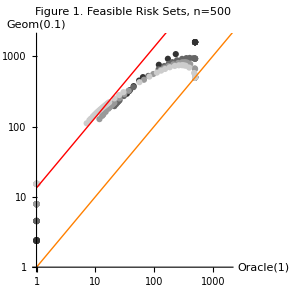

```mathematica
Show[f1LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Figure 2 Feasible risks for varying ω, with testimator oracle

```mathematica
id = With[
{α=0.1,β=0.1,scale=2,n=500},
makeID[α,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

f2Data=Table[getData[id⟦i⟧,2,""],{i,1,4}];
```

{{summary_risk_alpha10_beta10_omega05_scale2_n500,{0.1,0.1,0.05,2,500}},{summary_risk_alpha10_beta10_omega25_scale2_n500,{0.1,0.1,0.25,2,500}},{summary_risk_alpha10_beta10_omega50_scale2_n500,{0.1,0.1,0.5,2,500}},{summary_risk_alpha10_beta10_omega75_scale2_n500,{0.1,0.1,0.75,2,500}}}

found dimensions {42,8}

found dimensions {42,8}

found dimensions {42,8}

«1 more identical outputs»

Look for the angle where risk increases suddenly.

```mathematica
f2Data[[1,3]]//TableForm
```

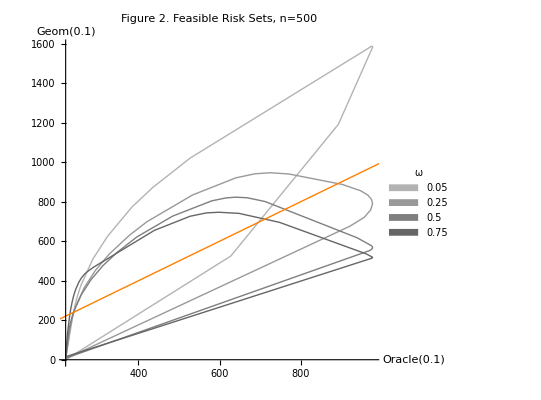

```mathematica
With[
{α=ToString[getAlpha[f2Data⟦1⟧]],
β=ToString[getBeta[f2Data⟦1⟧]]},
drawFeasibleSets[f2Data, 
"Figure 2. Feasible Risk Sets, n=500",
{StringJoin["Oracle(",α,")"],StringJoin["Geom(",β,")"]}]
]
```

Log scale is less interesting for these having seen them for the prior example.

```mathematica
f2LogPlots=Table[drawLogFeasibleSet[f2Data⟦i⟧,{False,colors⟦i⟧}],{i,1,4}]
```

```mathematica
Show[f2LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Figure 3 Paths within the feasible set, illustrating shape

This figure shows paths within the feasible set produced by non-zero means that occur with varying probabilities and varying sizes. The concave shape of the path within the feasible set shows that we are only gettin the convex boundary.  The figures require the data from figure 2 to show the boundary, then put these paths within that set.

```mathematica
stripCol[x_]:= #⟦{2,3}⟧&/@x

With[
{α=0.10,β=0.10,ω=0.5,scale=2,n=500},
With[
{path=StringJoin["~/C/bellman/figures/f3/risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]]},
Print[StringJoin[path,"/m0.5"]];
rr[0.5]=-stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[1.0]=-stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=-stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=-stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=-stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=-stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=-stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=-stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
]
]
```

~/C/bellman/figures/f3/risk_alpha10_beta10_omega50_scale2_n500/m0.5

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

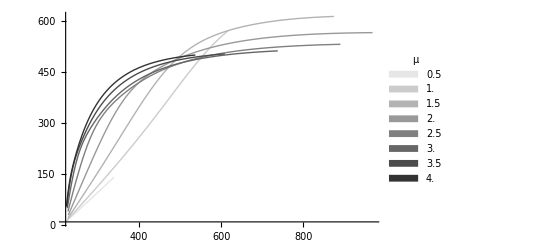

```mathematica
With[
{μ={0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0}},
lp=ListPlot[rr/@μ,
PlotRange->All,
Joined->True,PlotLegends->SwatchLegend[μ,LegendLabel->"μ"],
PlotStyle->GrayLevel/@Range[0.9,0.1,-0.1]]
]
```

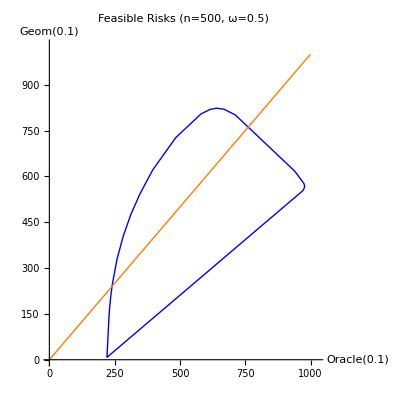

```mathematica
fp=drawFeasibleSet[f2Data⟦3⟧,{True,Blue}]
```

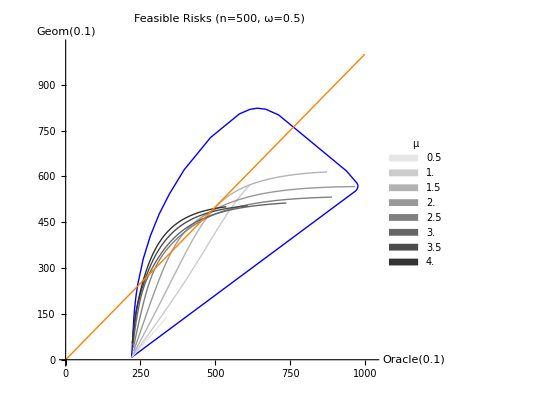

```mathematica
Show[fp,lp]
```

### Additional Plots Risk Inflation, Effects of number of tests

This plot shows the feasible set in a log-log plot to zoom in on the growth trajectory.  Probably should not have that diagonal arrow returning to the left since the set is not convex on the log-log scale.

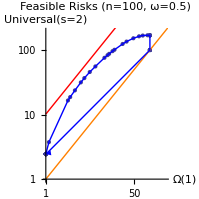
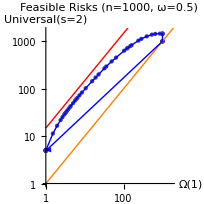
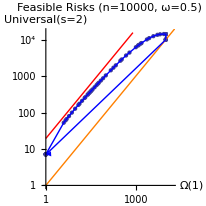
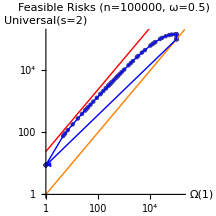

This is a plot to show the results for various values of n on the same graph. The align function rescales the oracle in the argument to match that in the reference set of coordinates.  Of course, all of the xy coordinate pairs (tables) need to be computed on the same grid.

```mathematica
(#⟦1⟧&/@xy[100])/(#⟦1⟧&/@xy[1000])xy[1000]
```

{{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1.,4.9781},{1.,7.46352},{1.,8.48179},{1.,9.09503},{1.,9.34627},{1.,9.54859},{1.,9.61351},{1.,9.6637},{1.,9.71541},{1.,9.76704},{1.,9.81115},{1.,9.83086},{1.,9.89444},{1.,9.92133},{1.,9.92079},{1.,9.91244},{1.,9.87986},{1.,9.81371},{1.14717,11.0705},{2.66802,24.7584},{2.94506,26.5979},{3.63303,31.9382},{4.72828,39.5592},{5.52181,45.2578},{7.02061,53.482},{9.00586,63.6606},{13.4679,82.3334},{15.4683,89.052},{16.5512,93.6673},{19.2555,102.521},{20.9676,108.264},{30.1292,129.591},{35.8269,140.711},{48.5095,156.406},{62.3546,161.448},{73.5121,160.915},{90.9595,152.964},{101.,145.346},{101,145.346},{101,145.346},{101,145.346},{101,145.346},{101,101.023},{101,101},{101,101},{101,101},{101,101},{101,101},{1.01568,4.95336},{1.00034,4.97694}}

```mathematica
Clear[ri];
ri[m_]:=With[
{ri=(#⟦2⟧/(2 Log[m] #⟦1⟧))& /@ (xy[m]),    (*  risk inflation as % of 2 log p *)
rpt=(#⟦1⟧/(2 Log[m]))& /@ (xy[m])                                               (* oracle risk per test *)
},
Sort[Transpose[{rpt,ri}],#1⟦1⟧≤#2⟦1⟧&]
]
```

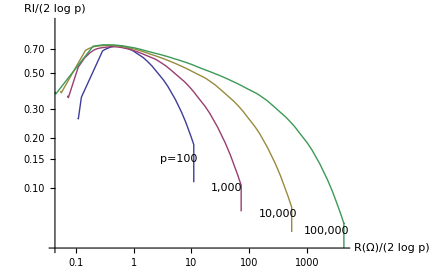

```mathematica
ListLogLogPlot[{ri[100],ri[1000],ri[10000],ri[100000]},
AxesLabel-> {"R(Ω)/(2 log p)","RI/(2 log p)"},
Epilog->{
Text["p=100",Log[{6,0.15}]],
Text["1,000",Log[{40,0.10}]],
Text["10,000",Log[{320,0.07}]],
Text["100,000",Log[{2150,0.055}]]},
Joined->True]
```